# Entanglement Distillation

See also Section 7.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Here, we start with a number of partially entangled pairs and “distills” a smaller number of maximally entangled pairs.

VonNeumannEntropy | VonNeumann entropy of a mixed state
PartialTrace | Partial trace over some subsystems
Dyad | Dyadic product of two vectors

Functions used in this document.

Make sure that the Q3 package is loaded.

```mathematica
<<Q3`
```

### Elementary Method

This is an elementary example with a small number of pairs.

The two parties are called Alice and Bob. Denote Alice’s qubits by A and Bob’s by B.

```mathematica
Let[Qubit,A,B]
```

Set the number $n of partially entangled pairs.

```mathematica
$n=4;
AA=A[Range[$n],None];
BB=B[Range[$n],None];
```

Check the total list of qubits on Alice’s and Bob’s sides all together.

```mathematica
AB=Join[AA,BB]
```

{A_1,A_2,A_3,A_4,B_1,B_2,B_3,B_4}

Let us first examine a single pair of partially entangled qubits in the following form. Parameter p tunes the extent of entanglement (p=1/2 is the maximally entangled case).

```mathematica
in=Ket[]Sqrt[1-p]+Ket[{A[1],B[1]}->1]*Sqrt[p];
LogicalForm[in]
```

√(1-p) 0_A_10_B_1+√p 1_A_11_B_1

For example, the reduced density operator for Alice’s qubit is obtained by tracing out Bob’s qubit.

```mathematica
rho=PartialTrace[in,B[1]];
Let[Real,p];
Matrix[rho]//MatrixForm
```

(1-p | 0
0 | p)

Calculate the von Neumann entropy associated with the reduced density operator, which tells you the entanglement extent in the partially entangled state in.

```mathematica
entropy=VonNeumannEntropy[rho]
```

((-1+p) Log[1-p])/Log[2]-(p Log[p])/Log[2]

Now, we consider $n partially entangled pairs with each pair in the state as above. Here is the explicit expression for the $n pairs of partially entangled pairs. Here, OTimes  is used just for better readability, and you can replace it with CircleTimes (⊗) or Multiply to get exactly the same result.

```mathematica
in=OTimes@@Table[Ket[]Sqrt[1-p]+Ket[{A[k],B[k]}->1]*Sqrt[p],{k,$n}];
LogicalForm[in]
```

(√(1-p) 0_A_10_B_1+√p 1_A_11_B_1)⊗(√(1-p) 0_A_20_B_2+√p 1_A_21_B_2)⊗(√(1-p) 0_A_30_B_3+√p 1_A_31_B_3)⊗(√(1-p) 0_A_40_B_4+√p 1_A_41_B_4)

Expanding it, one gets various terms all with identical parts on Alice’s and Bob’s side.

```mathematica
in=ReleaseTimes[in];
ProductForm[in,{AA,BB}]
```

(-1+p)^2 0000⊗0000+(1-p)^(3/2) √p 0001⊗0001+(1-p)^(3/2) √p 0010⊗0010-(-1+p) p 0011⊗0011+(1-p)^(3/2) √p 0100⊗0100-(-1+p) p 0101⊗0101-(-1+p) p 0110⊗0110+√(1-p) p^(3/2) 0111⊗0111+(1-p)^(3/2) √p 1000⊗1000-(-1+p) p 1001⊗1001-(-1+p) p 1010⊗1010+√(1-p) p^(3/2) 1011⊗1011-(-1+p) p 1100⊗1100+√(1-p) p^(3/2) 1101⊗1101+√(1-p) p^(3/2) 1110⊗1110+p^2 1111⊗1111

If Alice (or Bob) measures the total Z, i.e., Z=Z_1+Z_2+…+Z_n on her qubits, the possible outcomes are  m=0,1,…,n and the corresponding probabilities are given by the following formula.

```mathematica
prb[p_,m_]:=Binomial[$n,m]*(1-p)^($n-m)p^m
```

For fixed p (p=3/4), the probability distribution looks like the following plot. The highest probability is for m=np (m=3 in our case).

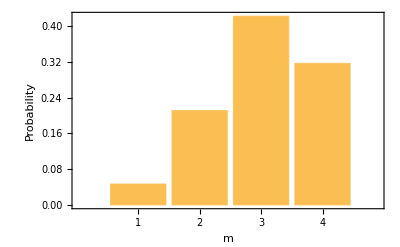

```mathematica
BarChart[
Table[prb[0.75,m],{m,$n}],
ChartLabels->Range[$n],
Axes->None,Frame->True,
FrameLabel->{"m","Probability"}
]
```

Given measurement outcome m, the post-measurement state is given by the following formula.

```mathematica
post[m_]:=Module[
{pp=Subsets[Range[$n],{m}],
aa,bb},
aa=Thread[A/@pp->1];
bb=Thread[B/@pp->1];
Total@MapThread[Ket,{aa,bb}]/Binomial[$n,m]//Garner
]
```

Assume that we have got outcome m=3.

```mathematica
$m=3;
```

The post-measurement state is then as follows.

```mathematica
out=post[$m];
out//ProductForm[#,{AA,BB}]&
```

1/4 0111⊗0111+1/4 1011⊗1011+1/4 1101⊗1101+1/4 1110⊗1110

Here, two points are worth noticing. First, the above state is spanned by four elements in the computational basis. As we will see soon below, this implies that we can encode (i.t., transform) this state into two pairs of qubits (2^2=4). Second, the coefficients are all the same. This means that when encoded in two pairs of qubits, the state in each pair is maximally entangled.

Too see these points, let us examine the supports of the density operators of Alice and Bob, respectively.

```mathematica
rhoA=PartialTrace[out,BB];
rhoB=PartialTrace[out,AA];
```

Observe that there are only four eigenstates with finite eigenvalue.

```mathematica
{val,vec}=ProperSystem[rhoA]
```

{{1/16,1/16,1/16,1/16,0,0,0,0,0,0,0,0,0,0,0,0},{1_A_11_A_21_A_3,1_A_11_A_21_A_4,1_A_11_A_31_A_4,1_A_21_A_31_A_4,1_A_11_A_21_A_31_A_4,1_A_11_A_2,1_A_11_A_3,1_A_11_A_4,1_A_1,1_A_21_A_3,1_A_21_A_4,1_A_2,1_A_31_A_4,1_A_3,1_A_4,␣}}

Get the basis spanning the support of the density operator ρ_A on Alice’s side (although this is already clear from the expression of vector out).

```mathematica
sppA=vec[[;;4]];
LogicalForm[sppA]
```

{1_A_11_A_21_A_30_A_4,1_A_11_A_20_A_31_A_4,1_A_10_A_21_A_31_A_4,0_A_11_A_21_A_31_A_4}

Similarly, get a basis spanning the support of the density operator ρ_B on Bob’s side (again, this is already clear from the expression of vector out).

```mathematica
{val,vec}=ProperSystem[rhoB];
sppB=vec[[;;4]];
LogicalForm[sppB]
```

{1_B_11_B_21_B_30_B_4,1_B_11_B_20_B_31_B_4,1_B_10_B_21_B_31_B_4,0_B_11_B_21_B_31_B_4}

Determine two qubits to store the maximally entangled pairs and construct the computational basis for those qubits on Alice’s side.

```mathematica
newA=Basis[A@{1,2}];
LogicalForm[newA]
```

{0_A_10_A_2,0_A_11_A_2,1_A_10_A_2,1_A_11_A_2}

Do the same thing on Bob’s side.

```mathematica
newB=Basis[B@{1,2}];
LogicalForm[newB]
```

{0_B_10_B_2,0_B_11_B_2,1_B_10_B_2,1_B_11_B_2}

Construct the transformation that would map the post-measurement state obtained above into the two destination qubits.

```mathematica
trs=Total[
MapThread[Dyad[#1,#2,AA]&,{newA,sppA}]**
MapThread[Dyad[#1,#2,BB]&,{newB,sppB}]
]
```

0_A_10_A_20_A_30_A_41_A_11_A_21_A_30_A_40_B_10_B_20_B_30_B_41_B_11_B_21_B_30_B_4+1_A_10_A_20_A_30_A_41_A_10_A_21_A_31_A_41_B_10_B_20_B_30_B_41_B_10_B_21_B_31_B_4+1_A_11_A_20_A_30_A_40_A_11_A_21_A_31_A_41_B_11_B_20_B_30_B_40_B_11_B_21_B_31_B_4+0_A_11_A_20_A_30_A_41_A_11_A_20_A_31_A_40_B_11_B_20_B_30_B_41_B_11_B_20_B_31_B_4

Finally, get the so-called distilled entanglement using the above transformation.

```mathematica
distilled=trs**out//LogicalForm
```

1/4 0_A_10_A_20_B_10_B_2+1/4 0_A_11_A_20_B_11_B_2+1/4 1_A_10_A_21_B_10_B_2+1/4 1_A_11_A_21_B_11_B_2

Check that the above state is a product of two pairs of maximally entangled states.

```mathematica
KetFactor[distilled]
```

1/4 (0_A_10_B_1+1_A_11_B_1)⊗(0_A_20_B_2+1_A_21_B_2)

So, we have successfully generated two maximally entangled pairs from four partially entangled pairs. Note that this was possible because we assumed that the measurement outcome was m=3. The case with m=1 is also handled following a similar procedure. However, if the measurement outcome is m=2, resulting in the post-measurement state

1/6 0011⊗0011+1/6 0101⊗0101+1/6 0110⊗0110+1/6 1001⊗1001+1/6 1010⊗1010+1/6 1100⊗1100

then there is no way to turn this state into a product state on a system of qubits.

Related Guides

Quantum Computation and Information

Related Tech Notes

Quantum Information Theory

Quantum Computation and Information: Overview

Related Links

J. Preskill (1998), Lecture Notes for Physics 229: Quantum Information and Computation.

M. Nielsen and I. L. Chuang (2022), Quantum Computation and Quantum Information (Cambridge University Press, 2011).

Mahn-Soo Choi (2022), A Quantum Computation Workbook (Springer, 2022).

## Metadata

### Categorization

Tech Note

QuantumWorkbook

QuantumWorkbook`

QuantumWorkbook/tutorial/EntanglementDistillation

### Keywords

quantum entanglement